## Panare 2DoF (RR):

```mathematica
Planare2dofITD[{qq1_,qq2_},x_,y_]:=Module[{hx,hy,JJ,hh,p,ll,F,q1,q2,T,L1,L2},
(*Verifico parametri*)
If[ListQ[qq1]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[qq2]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[x]!=False,Print["The argument 3 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];

T=0.01;
ll=1;
L1=1;
L2=1;
hx=L1*Cos[q1]+L2*Cos[q1+q2];
hy=L1*Sin[q1]+L2*Sin[q1+q2];

JJ={{D[hx,q1],D[hx,q2]},{D[hy,q1],D[hy,q2]}} ;

hh={{hx},{hy}} ;
p={{x},{y}} ;

F={{q1},{q2}}+T*ll*Inverse[JJ].(p-hh) /. {q1->qq1,q2->qq2} ;
Flatten[F]
]
```

```mathematica
Planare2dofIK[x_,y_]:=Module[{n,q1,q2,xx,yy},
(*Verifico parametri*)
If[ListQ[x]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

Subscript[s, 0]={10,1};
n=1000;
Do[Subscript[s, i]=Planare2dofITD[Subscript[s, i-1],x,y],{i,1,n}];

q1=Table[Subscript[s, i][[1]],{i,0,n}];
q2=Table[Subscript[s, i][[2]],{i,0,n}];
xx=Cos[q1]+Cos[q1+q2];
yy=Sin[q1]+Sin[q1+q2];
ListLinePlot[{xx,yy},PlotRange->All]
]
```

### test:

```mathematica
Planare2dofITD[{1,1},1/2,1/2]
```

{0.986392,1.026}

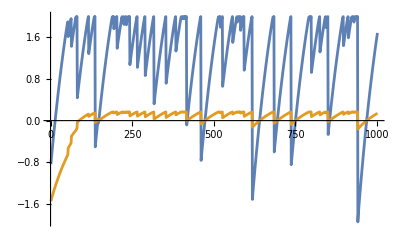

```mathematica
Planare2dofIK[1/2,1/2]
```